```mathematica
filesAR=FileNames["/home/carla//GDC/CONF/PHI/GDC_Conf_AR_PHI_ALL_Out/*.txt"];
dataAR=Map[Get[#]&, filesAR];
filesBR=FileNames["/home/carla//GDC/CONF/PHI/GDC_Conf_BR_PHI_ALL_Out/*.txt"];
dataBR=Map[Get[#]&, filesBR];
```

```mathematica
confAR=dataAR[[All,1]];
confBR=dataBR[[All,1]];
```

```mathematica
dojAR=confAR[[All,1]][[All,1]]
zAR=confAR[[All,2]][[All,1]]
fAR=confAR[[All,3]][[All,1]]
```

{0.000793021,0.00505051,0.0333333,0.0222222,0.0133333,0.04,1.}

{0.000515229,0.00478602,0.0322929,0.0216234,0.0129954,0.0396751,1.}

{0.481156,0.900476,0.939461,0.94752,0.950567,0.983888,1}

```mathematica
dojBR=confBR[[All,1]][[All,1]]
zBR=confBR[[All,2]][[All,1]]
fBR=confBR[[All,3]][[All,1]]
```

{0.000793021,0.00505051,0.0231729,0.0133333,0.0133333,0.0416667}

{0.000527404,0.00477249,0.0225747,0.0129954,0.0129994,0.0413448}

{0.498191,0.895651,0.949666,0.950567,0.95114,0.984669}

```mathematica
sList={2,3,4,5,6,7,8};
sList2={2.5,3.5,4.5,5.5,6.5,7.5};
ran=Range[Length[sList]];
ran2=Range[Length[sList2]];


dojPAR={#[[2]],#[[1]]}&/@Map[{dojAR[[#]],sList[[#]]}&,ran];
zPAR= {#[[2]],#[[1]]}&/@Map[{zAR[[#]],sList[[#]]}&,ran];
fPAR= {#[[2]],#[[1]]}&/@Map[{fAR[[#]],sList[[#]]}&, ran];
dojPBR={#[[2]],#[[1]]}&/@Map[{dojBR[[#]],sList2[[#]]}&,ran2];
zPBR= {#[[2]],#[[1]]}&/@Map[{zBR[[#]],sList2[[#]]}&, ran2];
fPBR= {#[[2]],#[[1]]}&/@Map[{fBR[[#]],sList2[[#]]}&,ran2];
```

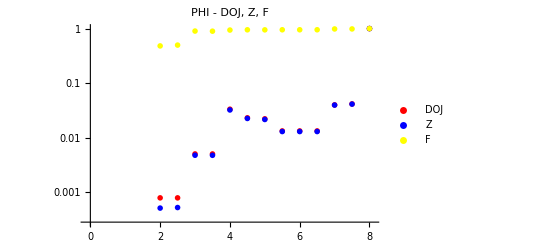

```mathematica
PlotAllParts=ListLogPlot[{Union[dojPAR,dojPBR], Union[zPAR,zPBR], Union[fPAR, fPBR]}, PlotLegends->{"DOJ","Z", "F"}, PlotRange->{{-0.1,8.1},All},PlotStyle-> {Red, Blue, Yellow}, PlotRange->All, PlotLabel->"PHI - DOJ, Z, F", PlotMarkers->{{"D",12},{"Z",12},{"F",12}}]
```

```mathematica
SetDirectory["/home/carla//GDC/CONF/PHI/"];
Put[Union[dojPAR,dojPBR],"PHI_DOJ.txt"]
Put[Union[zPAR,zPBR],"PHI_Z.txt"]
Put[Union[fPAR,fPBR],"PHI_F.txt"]
Export["PHI.jpeg",PlotAllParts,ImageSize->800, ImageResolution->300]
```

PHI.jpeg

```mathematica
(*PlotParts=ListPlot[{Union[dojPAR,dojPBR], Union[zPAR,zPBR], Union[fPAR, fPBR]}, PlotLegends->{"DOJ","Z", "F"}, PlotStyle-> {Red, Blue, Yellow}, PlotRange->{-0.001, 0.031},  PlotLabel->"PHI - DOJ, Z, F - Zoomed In",  PlotMarkers->{{"D",12},{"Z",12},{"F",12}}]
Export["PHI_Zoomed_In.jpeg",PlotParts,ImageSize->850]*)
```